For libration motion of the pendulum

```mathematica
Jl=Simplify[8/π(EllipticE[κ]-(1-κ)EllipticK[κ])/.κ->ϵ/2]
```

(8 EllipticE[ϵ/2]+4 (-2+ϵ) EllipticK[ϵ/2])/π

```mathematica
dJl=D[Jl,ϵ]//Simplify
```

(2 EllipticK[ϵ/2])/π

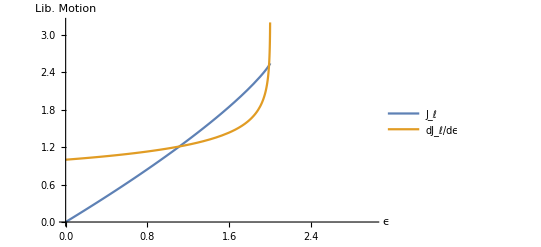

```mathematica
Plot[{Jl,dJl},{ϵ,0,3},PlotLegends->{"J_ℓ","dJ_ℓ/dϵ"},AxesLabel->{"ϵ","Lib. Motion"}]
lib=Plot[{Jl,dJl},{ϵ,0,3},PlotStyle->{Blue,Purple}];
```

For rotation motion of the pendulum

```mathematica
Jr=Simplify[(8 √κ)/π(EllipticE[κ^-1])/.κ->ϵ/2]
```

(4 √2 √ϵ EllipticE[2/ϵ])/π

```mathematica
dJr=D[Jr,ϵ]//Simplify
```

(2 √2 EllipticK[2/ϵ])/(π √ϵ)

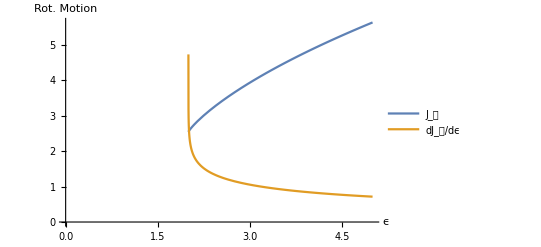

```mathematica
Plot[{Jr,dJr},{ϵ,0,5},PlotLegends->{"J_𝓇","dJ_𝓇/dϵ"},AxesLabel->{"ϵ","Rot. Motion"}]
rot=Plot[{Jr,dJr},{ϵ,0,5},PlotStyle->{Blue,Purple}];
```

Full motion of the pendulum

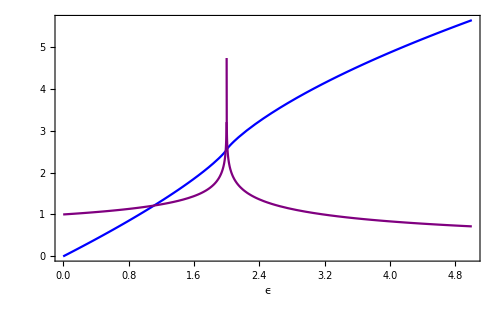

```mathematica
Show[lib,rot,PlotRange->All,Frame->True,FrameLabel->{Style["ϵ",Bold],""},Epilog->Inset[Column[{LineLegend[{Blue,Purple},{Style["J(ϵ)",12],Style["(dJ (ϵ))/dϵ",12]},LegendMarkerSize->{20,10}]}],Scaled[{0.2,0.7}]],ImageSize->500]
```